```mathematica
Quit[]
```

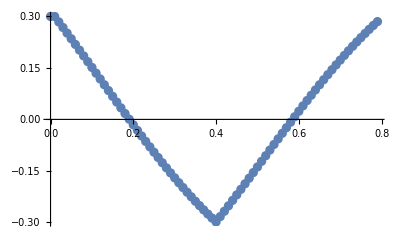

{A→-0.252084,ω→-7.87209,ϕ→4.6441}

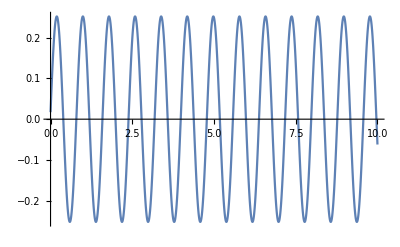

```mathematica
q = Flatten[Import["CPG_project/x_ref.csv"]][[1;;80]];
time = Table[i*0.01,{i,0,Length[q]-1}];
data = Thread[{time,q}];
scatter =ListPlot[data]
sol = FindFit[data,A*Sin[ω*t+ϕ] (*+B*Sin[ω2*t+ϕ2]*),{A,ω,ϕ},t,MaxIterations->1000,AccuracyGoal->6,PrecisionGoal->6]
approx[t_]:= A*Sin[ω*t+ϕ] (*+B*Sin[ω2*t+ϕ2]*);
Plot[approx[t]/.sol,{t,0,10}]
```